```mathematica
PoissonPlot[λ_,T_,i_,joined_,l_]:=Module[{vals,jumptimes,n=RandomInteger[PoissonDistribution[λ T]]},jumptimes=Sort[T*RandomReal[{0,1},n]];vals=Join[{0,0},Range[Length[jumptimes]]];Plot[Evaluate[Interpolation[Transpose[{Flatten[{0,jumptimes,T}],vals}],InterpolationOrder->0][x]-λ  l x],{x,0,T},PlotStyle->ColorData[1,i],Exclusions->If[joined,None,jumptimes],AxesLabel->{"Zeit","N"}]]
```

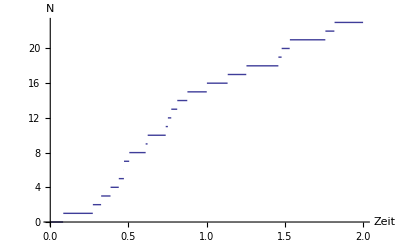

```mathematica
PoissonPlot[9,2,1,False,0]
```

```mathematica
Show[Table[PoissonPlot[5,1,1,joined,Boole[compensated]],{i,1,np}]
```

```mathematica
?Boole
```

RowBox[{"Boole", "[", StyleBox["expr", "TI"], "]"}] yields 1 if StyleBox["expr", "TI"] is True and 0 if it is False.